```mathematica
<<Local`QFTToolKit`
Put[SaveFile=NBname["stub"]<>".out"];
```

III.3.1

```mathematica
PR[CO["III.3.1: Show that in (1+1)-dimensional spacetime the Dirac field ψ has mass dimension 1/2, and hence the Fermi coupling(G) is dimensionless."],
NL,"● The Lagrangian: ",tmpS=ℒ->ψ̄ .(I T[γ,"u"][μ] . xPartialD[_,μ]+m).ψ+G(ψ̄ .ψ)^2,
NL,"In (1+1)-dimension theory: ",$sd= d->2,
NL,"• We have ",subd0= {dim[S]->0,dim[x]->-1,dim[m]->1};Column[subd0],
NL,"• dim[] Rules: ",
subd={dim[a_ . b_]->dim[a]+dim[b],dim[a_+b_]->dim[a],dim[OverBar[a_]]->dim[a],dim[a_ b_]->dim[a]+dim[b],dim[a_^n_]->n dim[a],dim[a_]:>0/;NumberQ[a]};Column[subd],

NL,"Dimensional calculation: ",
Yield,tmp=dim[tmpS[[2,2]]]+ dim[x^d]==0,
imply,tmp=tmp//.subd//.subd0,
imply,$d1=Solve[tmp,dim[ψ]][[1,1]]//Simplify;Framed[$d1/.$sd],

Yield,tmp=dim[tmpS[[2,1]]]+ dim[x^d]==0,
imply,tmp=tmp//.subd//.subd0,
imply,$d2=Solve[tmp,dim[G]][[1,1]]//Simplify;Framed[$d2/.$d1/.$sd]

]
```

III.3.1: Show that in (1+1)-dimensional spacetime the Dirac field ψ has mass dimension 1/2, and hence the Fermi coupling(G) is dimensionless.
● The Lagrangian: ℒ→G (ψ̄.ψ)^2+ψ̄.(m+ⅈ γ_μ^μ.UnderBar[∂]_μ[_]).ψ
In (1+1)-dimension theory: d→2
• We have dim[S]→0
dim[x]→-1
dim[m]→1
• dim[] Rules: dim[(a_).(b_)]→dim[a]+dim[b]
dim[a_+b_]→dim[a]
dim[OverBar[a_]]→dim[a]
dim[a_ b_]→dim[a]+dim[b]
dim[a_^n_]→n dim[a]
dim[a_]:>0/;NumberQ[a]
Dimensional calculation: 
→ dim[x^d]+dim[ψ̄.(m+ⅈ γ_μ^μ.UnderBar[∂]_μ[_]).ψ]==0 ⇒ 1-d+2 dim[ψ]==0 ⇒ dim[ψ]→1/2
→ dim[x^d]+dim[G (ψ̄.ψ)^2]==0 ⇒ -d+dim[G]+4 dim[ψ]==0 ⇒ dim[G]→0

III.3.2

```mathematica
PR[CO["● Derive (11): ",D->4-Subscript[B, E]-3/2 Subscript[F, E]," and (13): ",D->2->Subscript[F, E]/2," in (1+1)-dimensions."],
NL,"Check (5) in text: ",
$={L->Subscript[B, i]-(V-1),4V->Subscript[B, e]+2 Subscript[B, i],D->4L-2 Subscript[B, i]};Column[$],
yield,xEliminate[$,{L,V}],OK
]
```

● Derive (11): D→4-B_ⅇ-(3 F_ⅇ)/2 and (13): D→2→F_ⅇ/2 in (1+1)-dimensions.
Check (5) in text: L→1-V+B_13
4 V→2 B_13+B_e
D→4 L-2 B_13 ⟶ 4-B_e==D OK

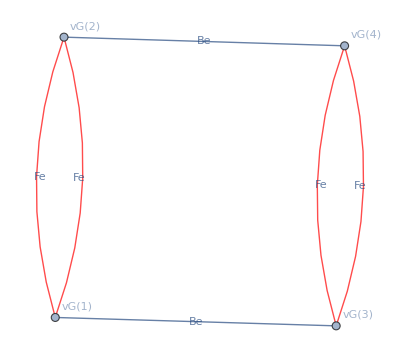
• Graphic routine for different diagrams: 
Number of λ vertices: 0 ⟶ 
Number of G vertices: 4 ⟶ {vG[1]<->Be[1],vG[1]<->Fe[1],vG[1]<->Fe[2]}
{vG[2]<->Be[2],vG[2]<->Fe[3],vG[2]<->Fe[4]}
{vG[3]<->Be[3],vG[3]<->Fe[5],vG[3]<->Fe[6]}
{vG[4]<->Be[4],vG[4]<->Fe[7],vG[4]<->Fe[8]}
Join end points: Fe[1]→Fe[3]
Fe[2]→Fe[4]
Fe[5]→Fe[7]
Fe[6]→Fe[8]
Be[2]→Be[4]
Be[1]→Be[3]

Graph data: (vG[1]<->vG[3]).EdgeLabels[Be]
(vG[2]<->vG[4]).EdgeLabels[Be]
(vG[1]<->vG[2]).EdgeLabels[Fe]
(vG[1]<->vG[2]).EdgeLabels[Fe]
(vG[3]<->vG[4]).EdgeLabels[Fe]
(vG[3]<->vG[4]).EdgeLabels[Fe]
-Graphics-

```mathematica
PR[CG["• Graphic routine for different diagrams: "],
$pairλ={};$pairG={};$pairλG={}; $nbe=0;$nfe=0;
NL,"Number of λ vertices: ",$nvλ=0,(**)
yield,$λ=Table[UndirectedEdge[vλ[IntegerPart[1+(i-1)/4]],Be[$nbe=i]],{i,1,$nvλ*4}];Column[$λ],
NL,"Number of G vertices: ",$nvG=4,(**)
yield,$f=Table[{UndirectedEdge[vG[i],Be[++$nbe]],UndirectedEdge[vG[i],Fe[++$nfe]],UndirectedEdge[vG[i],Fe[++$nfe]]},{i,1,$nvG}];Column[$f],"PON",
NL,"Join end points: ",(**)
$join={
Fe[1]->Fe[3],
Fe[2]->Fe[4],
Fe[5]->Fe[7],
Fe[6]->Fe[8],
Be[2]->Be[4],
Be[1]->Be[3](*,
Be[4]->Be[14],
Be[11]->Be[13],
Fe[1]->Fe[3]*)
};Column[$join],"POFF",
NL,"Construct Graph data: ",
$0=$={$f,$λ}/.$join//Flatten;
NL,"Remove common endpoints, Be,Fe: ",
For[i=1,i≤Length[$0],i++,If[Count[$0,$$=UndirectedEdge[_,Be[i]]]>1,AppendTo[$pairλ,$$]]];
For[i=1,i≤Length[$0],i++,If[Count[$0,$$=UndirectedEdge[_,Fe[i]]]>1,AppendTo[$pairG,$$]]];
NL,"2 Be[],Fe[]'s list: ",$pair=Join[$pairλ,$pairG],
NL,"End point Pairs: ",$=Cases[$0,#]&/@$pair;Column[$],
NL,"Position of Pair elements: ",$pos=ExtractPositionPattern[$0,Flatten[$pair]],
NL,"VV pairs with common Be[]: ",
$vv=$
//.{UndirectedEdge[v1:vλ_[i1_],Be[k_]],UndirectedEdge[v2:vλ_[i2_],Be[k_]]}->Style[UndirectedEdge[v1,v2],Thick].EdgeLabels[Be]
//.{UndirectedEdge[vG[i1_],Fe[k_]],UndirectedEdge[vG[i2_],Fe[k_]]}->Style[UndirectedEdge[vG[i1],vG[i2]], Red,Thick].EdgeLabels[Fe]
//.{UndirectedEdge[vλ[i1_],Be[k_]],UndirectedEdge[vG[i2_],Be[k_]]}->Style[UndirectedEdge[vλ[i1],vG[i2]],Thick].EdgeLabels[Be]//.{UndirectedEdge[vG[i1_],Be[k_]],UndirectedEdge[vλ[i2_],Be[k_]]}->Style[UndirectedEdge[vG[i1],vλ[i2]],Thick].EdgeLabels[Be],
NL,"Delete List: ",$del=Map[First[#]&,$pos],
NL,$=Delete[$0,$del],"PON",
NL,$=Append[$,$vv]//Flatten;
NL,"Graph data: ",$gdata=$=$/.uu:UndirectedEdge[a_,b_]:>Style[uu,Red]/;!FreeQ[{a,b},Fe]/.uu:UndirectedEdge[a_,b_]:>Style[uu,Thin]/;!FreeQ[{a,b},Be];Column[$],"POFF",
NL,"Collect edge info: ",
$edge=ExtractPattern[a_ . EdgeLabels[_]][$];
$edge=$edge/.a_ . EdgeLabels[b_]->(a->b)/.Style[a_,b__]->a;
Yield,$=$/.b_ .EdgeLabels[a_]->b;
"PON",
NL,$g=Graph[$,VertexLabels->"Name",EdgeLabels->$edge]
]
```

```mathematica
PR[CG["• Evaluate Graph: "],
$fi=0;
NL,"Edges: ",$edges=EdgeList[$g],$edges=$edges/.UndirectedEdge->List;
NL,"Bi count: ",$bi=Length[ExtractPattern[EdgeLabels[Be]][$gdata]],
NL,"Be count: ",$Be=Count[Flatten[$edges],Be[_]],
NL,"Number λ-vertices: ",$nvλ=Count[DeleteDuplicates[Flatten[$edges]],vλ[_]],
NL,"Fi count: ",$fi=Length[ExtractPattern[EdgeLabels[Fe]][$gdata]],
NL,"Fe count: ",$Fe=Count[Flatten[$edges],Fe[_]],
NL,"Number G-vertices: ",$nvG=Count[DeleteDuplicates[Flatten[$edges]],vG[_]],
NL,
NL,"Check: ",CO[$=HoldForm[2$nvG==$Fe+2 $fi]],yield,ReleaseHold[$],
NL,"Check (10): ",$=HoldForm[$nvG+4 $nvλ== $Be+2$bi];CO[$],$=ReleaseHold[$];If[$," (OK)"," (NO)"],
NL,"Check (6): ",CO[$L=Loops ->$bi+$fi-($nvλ+$nvG-1)],OK,
NL,"Check (8): ",CO[($=HoldForm[  D->4 L -2 $bi-$fi])->ReleaseHold[$]]
]
PR[CG["• Determine D(degree of Divergence) (11): "],
NL,"We have the relationships: ",
$={D==4L-2Bi-Fi,2Vg==Fe+2 Fi,Vg+4 Vλ== Be+2 Bi,L==Bi+Fi-(Vλ+Vg-1)};Column[$],
CO["momentum(k) contribution of Fi to D: 1/k"],
$=xEliminate[$,{Bi,Fi,L}];
Yield,$=Solve[$,D]//First//First//Simplify;Framed[$],back,"(11)"
]
```

• Evaluate Graph: 
Edges: {vG[1]<->vG[3],vG[2]<->vG[4],vG[1]<->vG[2],vG[1]<->vG[2],vG[3]<->vG[4],vG[3]<->vG[4]}
Bi count: 2
Be count: 0
Number λ-vertices: 0
Fi count: 4
Fe count: 0
Number G-vertices: 4

Check: 2 $nvG==$Fe+2 $fi ⟶ True
Check (10): $nvG+4 $nvλ==$Be+2 $bi (OK)
Check (6): Loops→3 OK 
Check (8): (D→4 L-2 $bi-$fi)→D→-8+4 L

• Determine D(degree of Divergence) (11): 
We have the relationships: D==-2 Bi-Fi+4 L
2 Vg==Fe+2 Fi
Vg+4 Vλ==Be+2 Bi
L==1+Bi+Fi-Vg-Vλmomentum(k) contribution of Fi to D: 1/k
→ D→4-Be-(3 Fe)/2 ⟵(11)

```mathematica
PR[CG["● To Determine D(degree of Divergence) in 1+1-dimensions(13): "],
NL,"The relationships are: ",
$={D==4L-Fi,4Vg==Fe+2 Fi,L==Fi-(Vg-1)};Column[$],
CO[" momentum(k) contribution of Fi to D: 1/k"],
$=xEliminate[$,{Fi,L}];
Yield,$=Solve[$,D]//First//First//Simplify;Framed[$],back,"(12)",
NL,"• for 1+1 dimensions the relationships: ",
$={D==2L-Fi,4Vg==Fe+2 Fi,L==Fi-(Vg-1)};Column[$],
$=xEliminate[$,{Fi,L}];
Yield,$=Solve[$,D]//First//First//Simplify;Framed[$],back,"(13)"
]
```

● To Determine D(degree of Divergence) in 1+1-dimensions(13): 
The relationships are: D==-Fi+4 L
4 Vg==Fe+2 Fi
L==1+Fi-Vg momentum(k) contribution of Fi to D: 1/k
→ D→4-(3 Fe)/2+2 Vg ⟵(12)
• for 1+1 dimensions the relationships: D==-Fi+2 L
4 Vg==Fe+2 Fi
L==1+Fi-Vg
→ D→2-Fe/2 ⟵(13)

III.3.4

```mathematica
PR[CO["III.3.4: Convince yourself that δm is logarithmically divergent to any finite order in perturbation theory"],
NL,"• Mass corrections involve at least 2 propagators. Two fermionic propagators in a perturbation loop will have the more divergent contribution to the Feynmann integral.  However, fermionic propagators have a factor of momentum in the numerator which cancel when integrated over the range of the Feynman integral. The product of loops contribute product of these logarthimic factors. "
]
```

III.3.4: Convince yourself that δm is logarithmically divergent to any finite order in perturbation theory
• Mass corrections involve at least 2 propagators. Two fermionic propagators in a perturbation loop will have the more divergent contribution to the Feynmann integral.  However, fermionic propagators have a factor of momentum in the numerator which cancel when integrated over the range of the Feynman integral. The product of loops contribute product of these logarthimic factors.